### Coupled Differential Equations https://www.youtube.com/watch?v=p-4BiFcungc

```mathematica
sol = DSolve[
{
x'[t] == -2 y[t] x[t],
y'[t] == x[t]y[t]
},
{x[t], y[t]}, t
]
```

{{y[t]→C[1]+C[1]/(-1+ⅇ^(2 C[1] (t+C[2]))),x[t]→-(2 C[1])/(-1+ⅇ^(2 C[1] (t+C[2])))}}

```mathematica
sol = DSolve[
{
x'[t] == -2 y[t] x[t],
y'[t] == x[t]y[t],
x[0] ==1, y[0] ==2
},
{x[t], y[t]}, t
]
```

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

{{y[t]→(10 ⅇ^(5 t))/(1+4 ⅇ^(5 t)),x[t]→5/(1+4 ⅇ^(5 t))}}

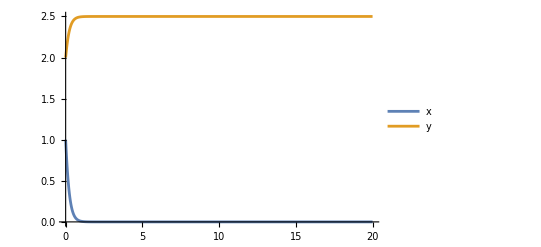

```mathematica
Plot[Evaluate[
{{x[t], y[t]}/.sol}], {t, 0, 20}, 
PlotRange->All, PlotLegends->{"x","y"}
]
```

### Numeric Solving

```mathematica
a = 0.5; b=1.5; c=2; d=3;
```

```mathematica
sol = NDSolve[
{
x'[t] == a x[t] - b y[t] x[t],
y'[t] == c x[t]y[t] - d y[t],
x[0] ==2, y[0] ==1
},
{x[t], y[t]}, {t, 0, 20}
]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

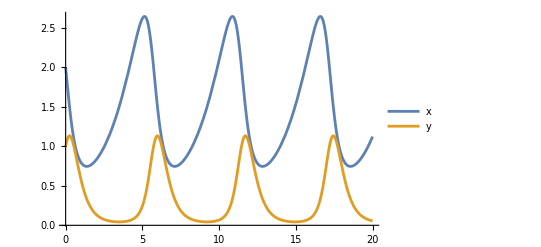

```mathematica
Plot[Evaluate[{x[t],y[t]} /. sol], {t, 0 ,20}, PlotRange->All, PlotLegends->{"x", "y"}]
```

```mathematica
a=.;b=.;c=.;d=.;
Manipulate[
sol = NDSolve[
{
x'[t] == a x[t] - b y[t] x[t],
y'[t] == c x[t]y[t] - d y[t],
x[0] ==2, y[0] ==1
},
{x[t], y[t]}, {t, 0, 20}
];
Plot[Evaluate[{x[t],y[t]} /. sol], {t, 0 ,20}, PlotRange->All, PlotLegends->{"x", "y"}],
{a,0,2,0.1}, {b, 0, 2, 0.1}, {c, 0, 2, 0.1},{d, 0, 2, 0.1}
]
```

NDSolve::dsvar: 0.5 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.5]==2. x[0.5]-1. x[0.5] y[0.5],y'[0.5]==-1. y[0.5]+1. x[0.5] y[0.5],x[0]==2,y[0]==1},{x[0.5],y[0.5]},{0.5,0,20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.5 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x'[0.5]==2. x[0.5]-1. x[0.5] y[0.5],y'[0.5]==-1. y[0.5]+1. x[0.5] y[0.5],x[0.]==2.,y[0.]==1.},{x[0.5],y[0.5]},{0.5,0.,20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.5 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[0.5]==2. x[0.5]-1. x[0.5] y[0.5],y'[0.5]==-1. y[0.5]+1. x[0.5] y[0.5],x[0.]==2.,y[0.]==1.},{x[0.5],y[0.5]},{0.5,0.,20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.